```mathematica
expr1p = expr1 (β Exp[β (ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2;
expr2p = expr2 (β Exp[β (ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2;
```

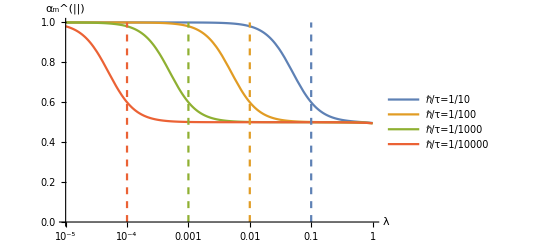

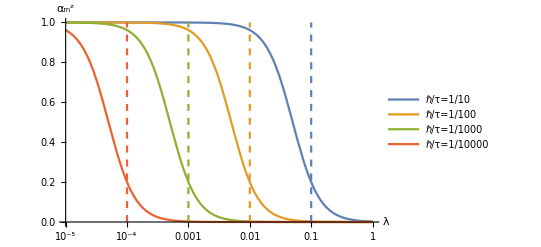

```mathematica
nsub = {Δ->0,nx->1,nz->0,ϵ->μ,μ->10};

coeff[αp_,expr_]:=expr//.nsub/.{α->αp}
SetAttributes[coeff,Listable];

iτs = Table[10^-n,{n,{1,2,3,4}}];
iτslabels = {HoldForm[ℏ/τ = 1/10],HoldForm[ℏ/τ = 1/100],HoldForm[ℏ/τ = 1/1000],HoldForm[ℏ/τ = 1/10000]};
αs = 1/(π ϵ //.nsub)iτs;
lines =  Table[{{iτ,0.0},{iτ,1}},{iτ,iτs}];
LogLinearPlot[Evaluate@coeff[αs,expr1],{λ,10^-5,1},PlotRange->{{10^-5,1},{0,1}},PlotLegends->iτslabels,AxesLabel->{"λ","α_m^(||)"}];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]

LogLinearPlot[Evaluate@coeff[αs,expr2],{λ,10^-5,1},PlotRange->{{10^-5,1},{0,1}},PlotLegends->iτslabels,AxesLabel->{"λ","α_m^z"}];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]
```

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at ϵ = 160..

General::stop: Further output of NIntegrate::ncvs will be suppressed during this calculation.

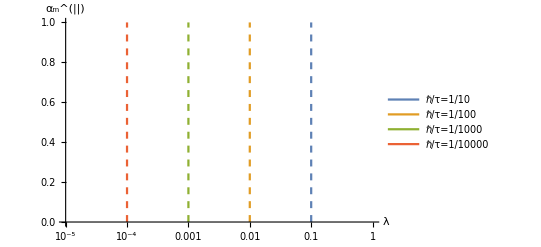

```mathematica
ClearAll[β,λ]
coeff[αp_,expr_,βp_,λp_]:=Block[{tmp, range},tmp = expr//.{μ->10,Δ->0,nz->0,nx->1,β->βp,λ->λp}/.{α->αp};
range = {μ-15/β,μ+15/β}/.μ->10/.β->βp;
NIntegrate[tmp,{ϵ,range[[1]],range[[2]]},Exclusions->{λp,-λp},Method->"DoubleExponential"];
]

LogLinearPlot[Evaluate@coeff[αs,expr1p, 0.1,λ],{λ,10^-5,1},PlotRange->{{10^-5,1},{0,1}},PlotLegends->iτslabels,AxesLabel->{"λ","α_m^(||)"}];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]
```

(0.05 ⅇ^(0.1 (ϵ-10)) (0.00098696 (2 ϵ^2-0.03) ϵ^2+0.04 (ϵ^2-0.02)))/((ⅇ^(0.1 (ϵ-10))+1)^2 (ϵ-0.1) (ϵ+0.1) (0.00098696 ϵ^2+0.04))

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (0.1 | 160.). NIntegrate obtained 0.843469 and 0.0000226284 for the integral and error estimates.

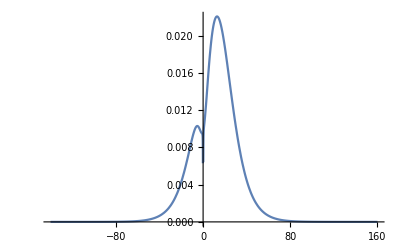

```mathematica
λp=0.1;βp=0.1;αp=0.01;
tmp = expr1p//.{μ->10,Δ->0,nz->0,nx->1,β->βp,λ->λp}/.{α->αp}
range = {μ-15/β,μ+15/β}/.μ->10/.β->βp;
NIntegrate[tmp,{ϵ,range[[1]],range[[2]]},Exclusions->{λp,-λp},Method->"DoubleExponential"];
Plot[tmp,{ϵ,range[[1]],range[[2]]},PlotRange->All]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (0.091 | 160.). NIntegrate obtained 0.546984 and 0.0000177354 for the integral and error estimates.

0.546984

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-0.00501187 | 0.00501187). NIntegrate obtained 0.912343 and 1.67241×10^-6 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-0.00794328 | 0.00794328). NIntegrate obtained 0.869936 and 2.0363×10^-6 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (0.01 | 160.). NIntegrate obtained 0.843467 and 9.58297×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

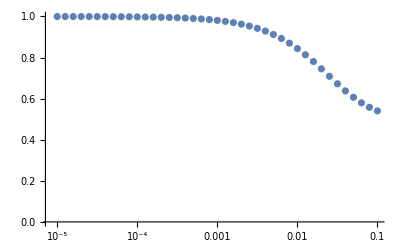

```mathematica
myexpr[expr_,μp_,βp_,λp_,αp_]:=Block[{range},
range=range = {μ-15/β,μ+15/β}/.μ->μp/.β->βp;NIntegrate[expr/.{β->βp,λ->λp,α->αp,μ->μp},{ϵ,range[[1]],range[[2]]},Exclusions->{-λp,λp},Method->"DoubleExponential"]
]
SetAttributes[myexpr,Listable];

myexpr[expr1p,10,0.1,0.091,0.001]
λs = Table[10^n,{n,-5,-1,0.1}];
ListLogLinearPlot[Transpose[{λs,Table[myexpr[expr1p,10,0.1,λ,0.001],{λ,λs}]}],PlotRange->{0,1}]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-0.00501187 | 0.00501187). NIntegrate obtained 0.970176 and 1.67241×10^-6 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-0.00794328 | 0.00794328). NIntegrate obtained 0.953743 and 2.0363×10^-6 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (0.01 | 160.). NIntegrate obtained 0.942634 and 9.58297×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

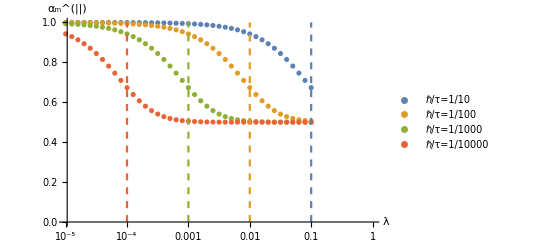

```mathematica
iτs = Table[10^-n,{n,{1,2,3,4}}];
iτslabels = {HoldForm[ℏ/τ = 1/10],HoldForm[ℏ/τ = 1/100],HoldForm[ℏ/τ = 1/1000],HoldForm[ℏ/τ = 1/10000]};
αs = 1/(π ϵ //.nsub)iτs;
lines =  Table[{{iτ,0.0},{iτ,1}},{iτ,iτs}];
ListLogLinearPlot[Evaluate@Table[Transpose[{λs,Table[myexpr[expr1p,10,0.1,λ,α],{λ,λs}]}],{α,αs}],
PlotRange->{{10^-5,1},{0,1}},
PlotLegends->iτslabels,AxesLabel->{"λ","α_m^(||)"}];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-0.0316228 | 0.0316228). NIntegrate obtained 0.53234 and 1.41003×10^-6 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (0.0398107 | 1510.). NIntegrate obtained 0.521975 and 5.31745×10^-7 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-0.0501187 | 0.0501187). NIntegrate obtained 0.514636 and 9.87855×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

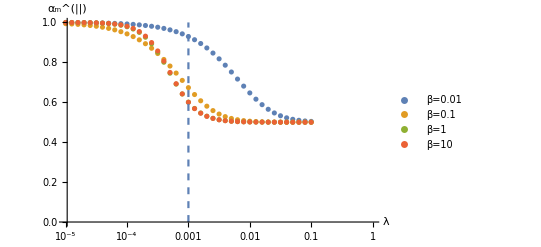

```mathematica
iτs = Table[10^-n,{n,{1,2,3,4}}];
iτslabels = {HoldForm[ℏ/τ = 1/10],HoldForm[ℏ/τ = 1/100],HoldForm[ℏ/τ = 1/1000],HoldForm[ℏ/τ = 1/10000]};
α= 1/(π ϵ //.nsub)10^-3;
βs = {0.01,0.1,1,10};
βlabels = {"β=0.01","β=0.1","β=1","β=10"};

lines =  {{10^-3,0.0},{10^-3,1}};
ListLogLinearPlot[Evaluate@Table[Transpose[{λs,Table[myexpr[expr1p,10,β,λ,α],{λ,λs}]}],{β,βs}],
PlotRange->{{10^-5,1},{0,1}},
PlotLegends->βlabels,AxesLabel->{"λ","α_m^(||)"}];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]
```

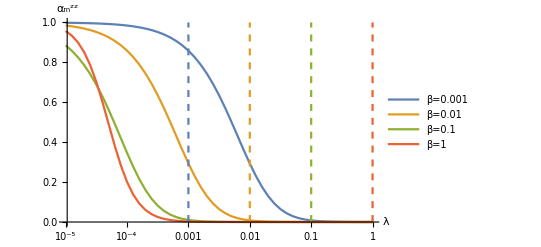

```mathematica
λs = Table[10^n,{n,-5,0,0.1}];
iτs = Table[10^-n,{n,{1,2,3,4}}];
iτslabels = {HoldForm[ℏ/τ = 1/10],HoldForm[ℏ/τ = 1/100],HoldForm[ℏ/τ = 1/1000],HoldForm[ℏ/τ = 1/10000]};
α= 1/(π ϵ //.nsub)10^-4;
βs = {0.001,0.01,0.1,1};
βlabels = {"β=0.001","β=0.01","β=0.1","β=1"};

lines =  Table[{{iτ,0.0},{iτ,1}},{iτ,βs}];

ListLogLinearPlot[Evaluate@Table[Transpose[{λs,Table[myexpr[expr2p,10,β,λ,α],{λ,λs}]}],{β,βs}],
PlotRange->{{10^-5,1},{0,1}},
PlotLegends->βlabels,AxesLabel->{"λ","α_m^zz"},Joined->True];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-14990. | -0.125893). NIntegrate obtained 0.502541 and 6.49367×10^-7 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-14990. | -0.199526). NIntegrate obtained 0.501024 and 8.12952×10^-7 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-0.251189 | 0.251189). NIntegrate obtained 0.500648 and 5.73426×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

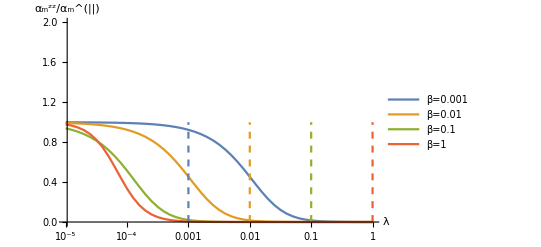

```mathematica
λs = Table[10^n,{n,-5,0,0.1}];
iτs = Table[10^-n,{n,{1,2,3,4}}];
iτslabels = {HoldForm[ℏ/τ = 1/10],HoldForm[ℏ/τ = 1/100],HoldForm[ℏ/τ = 1/1000],HoldForm[ℏ/τ = 1/10000]};
α= 1/(π ϵ //.nsub)10^-4;
βs = {0.001,0.01,0.1,1};
βlabels = {"β=0.001","β=0.01","β=0.1","β=1"};

lines =  Table[{{iτ,0.0},{iτ,1}},{iτ,βs}];

ListLogLinearPlot[Evaluate@Table[Transpose[{λs,Table[myexpr[expr2p,10,β,λ,α]/myexpr[expr1p,10,β,λ,α],{λ,λs}]}],{β,βs}],
PlotRange->{{10^-5,1},{0,2}},
PlotLegends->βlabels,AxesLabel->{"λ","α_m^zz/α_m^(||)"},Joined->True];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]
```

```mathematica
βs = {0.001,0.01,0.1,1};
βlabels = {"β=0.001","β=0.01","β=0.1","β=1"};
```

```mathematica
curves1 = Table[Transpose[
{λs,Table[myexpr[expr1p,10,β,λ,α],{λ,λs}]}],
{β,βs}]
curves2 = Table[Transpose[
{λs,Table[myexpr[expr2p,10,β,λ,α],{λ,λs}]}],
{β,βs}]
curves = Join[curves1, curves2];
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-14990. | -0.125893). NIntegrate obtained 0.502541 and 6.49367×10^-7 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-14990. | -0.199526). NIntegrate obtained 0.501024 and 8.12952×10^-7 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (-0.251189 | 0.251189). NIntegrate obtained 0.500648 and 5.73426×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

({0.00001,0.999215} | {0.0000125893,0.999012} | {0.0000158489,0.998757} | {0.0000199526,0.998436} | {0.0000251189,0.998032} | {0.0000316228,0.997524} | {0.0000398107,0.996886} | {0.0000501187,0.996084} | {0.0000630957,0.995078} | {0.0000794328,0.993814} | {0.0001,0.99223} | {0.000125893,0.990246} | {0.000158489,0.987763} | {0.000199526,0.984662} | {0.000251189,0.980797} | {0.000316228,0.975992} | {0.000398107,0.970036} | {0.000501187,0.962684} | {0.000630957,0.953652} | {0.000794328,0.942624} | {0.001,0.929262} | {0.00125893,0.913221} | {0.00158489,0.894182} | {0.00199526,0.871899} | {0.00251189,0.846252} | {0.00316228,0.817324} | {0.00398107,0.785465} | {0.00501187,0.751342} | {0.00630957,0.71595} | {0.00794328,0.68055} | {0.01,0.646541} | {0.0125893,0.61526} | {0.0158489,0.587782} | {0.0199526,0.564754} | {0.0251189,0.546338} | {0.0316228,0.532252} | {0.0398107,0.521914} | {0.0501187,0.514594} | {0.0630957,0.509566} | {0.0794328,0.506197} | {0.1,0.50398} | {0.125893,0.502541} | {0.158489,0.501614} | {0.199526,0.501024} | {0.251189,0.500648} | {0.316228,0.50041} | {0.398107,0.500261} | {0.501187,0.500164} | {0.630957,0.500104} | {0.794328,0.500066} | {1.,0.500129}
{0.00001,0.992249} | {0.0000125893,0.990269} | {0.0000158489,0.987793} | {0.0000199526,0.984699} | {0.0000251189,0.980843} | {0.0000316228,0.976049} | {0.0000398107,0.970106} | {0.0000501187,0.96277} | {0.0000630957,0.953757} | {0.0000794328,0.942751} | {0.0001,0.929414} | {0.000125893,0.913401} | {0.000158489,0.894392} | {0.000199526,0.87214} | {0.000251189,0.846523} | {0.000316228,0.817621} | {0.000398107,0.785781} | {0.000501187,0.751668} | {0.000630957,0.716274} | {0.000794328,0.680859} | {0.001,0.646822} | {0.00125893,0.615504} | {0.00158489,0.587984} | {0.00199526,0.564914} | {0.00251189,0.546461} | {0.00316228,0.53234} | {0.00398107,0.521973} | {0.00501187,0.514636} | {0.00630957,0.509594} | {0.00794328,0.506211} | {0.01,0.503989} | {0.0125893,0.502548} | {0.0158489,0.501618} | {0.0199526,0.501027} | {0.0251189,0.50065} | {0.0316228,0.50041} | {0.0398107,0.500259} | {0.0501187,0.500163} | {0.0630957,0.500106} | {0.0794328,0.500067} | {0.1,0.500044} | {0.125893,0.500027} | {0.158489,0.500015} | {0.199526,0.500012} | {0.251189,0.500003} | {0.316228,0.500007} | {0.398107,0.500032} | {0.501187,0.499952} | {0.630957,0.500038} | {0.794328,0.500051} | {1.,0.500898}
{0.00001,0.942634} | {0.0000125893,0.929128} | {0.0000158489,0.91285} | {0.0000199526,0.893447} | {0.0000251189,0.870636} | {0.0000316228,0.844272} | {0.0000398107,0.814423} | {0.0000501187,0.781468} | {0.0000630957,0.746157} | {0.0000794328,0.709617} | {0.0001,0.673284} | {0.000125893,0.638727} | {0.000158489,0.607399} | {0.000199526,0.580385} | {0.000251189,0.558238} | {0.000316228,0.540946} | {0.000398107,0.52804} | {0.000501187,0.518784} | {0.000630957,0.512366} | {0.000794328,0.508034} | {0.001,0.505169} | {0.00125893,0.503305} | {0.00158489,0.502102} | {0.00199526,0.501333} | {0.00251189,0.500845} | {0.00316228,0.500534} | {0.00398107,0.500335} | {0.00501187,0.500214} | {0.00630957,0.500134} | {0.00794328,0.500086} | {0.01,0.500053} | {0.0125893,0.500035} | {0.0158489,0.500024} | {0.0199526,0.500016} | {0.0251189,0.500013} | {0.0316228,0.499968} | {0.0398107,0.499981} | {0.0501187,0.49998} | {0.0630957,0.499992} | {0.0794328,0.499996} | {0.1,0.500001} | {0.125893,0.499811} | {0.158489,0.499774} | {0.199526,0.499996} | {0.251189,0.499883} | {0.316228,0.499901} | {0.398107,0.49992} | {0.501187,0.499818} | {0.630957,0.500577} | {0.794328,0.500982} | {1.,0.507963}
{0.00001,0.97853} | {0.0000125893,0.967035} | {0.0000158489,0.950095} | {0.0000199526,0.925947} | {0.0000251189,0.893053} | {0.0000316228,0.850843} | {0.0000398107,0.800558} | {0.0000501187,0.745628} | {0.0000630957,0.691006} | {0.0000794328,0.641575} | {0.0001,0.600577} | {0.000125893,0.569015} | {0.000158489,0.546121} | {0.000199526,0.530239} | {0.000251189,0.519565} | {0.000316228,0.512547} | {0.000398107,0.508} | {0.000501187,0.505081} | {0.000630957,0.503219} | {0.000794328,0.502037} | {0.001,0.501287} | {0.00125893,0.500813} | {0.00158489,0.500513} | {0.00199526,0.500324} | {0.00251189,0.500204} | {0.00316228,0.500129} | {0.00398107,0.500081} | {0.00501187,0.500051} | {0.00630957,0.500032} | {0.00794328,0.50002} | {0.01,0.500012} | {0.0125893,0.500007} | {0.0158489,0.500003} | {0.0199526,0.500001} | {0.0251189,0.499998} | {0.0316228,0.499995} | {0.0398107,0.499992} | {0.0501187,0.499986} | {0.0630957,0.499977} | {0.0794328,0.499964} | {0.1,0.499943} | {0.125893,0.499909} | {0.158489,0.499857} | {0.199526,0.499773} | {0.251189,0.49964} | {0.316228,0.49943} | {0.398107,0.499097} | {0.501187,0.498567} | {0.630957,0.497727} | {0.794328,0.496386} | {1.,0.494267})

({0.00001,0.99843} | {0.0000125893,0.998025} | {0.0000158489,0.997514} | {0.0000199526,0.996872} | {0.0000251189,0.996065} | {0.0000316228,0.995049} | {0.0000398107,0.993773} | {0.0000501187,0.99217} | {0.0000630957,0.990156} | {0.0000794328,0.987629} | {0.0001,0.984461} | {0.000125893,0.980492} | {0.000158489,0.975527} | {0.000199526,0.969325} | {0.000251189,0.961595} | {0.000316228,0.951984} | {0.000398107,0.940073} | {0.000501187,0.925368} | {0.000630957,0.907304} | {0.000794328,0.88525} | {0.001,0.858525} | {0.00125893,0.826443} | {0.00158489,0.788366} | {0.00199526,0.743799} | {0.00251189,0.692506} | {0.00316228,0.63465} | {0.00398107,0.57093} | {0.00501187,0.502684} | {0.00630957,0.431899} | {0.00794328,0.361101} | {0.01,0.293083} | {0.0125893,0.230522} | {0.0158489,0.175565} | {0.0199526,0.12951} | {0.0251189,0.0926767} | {0.0316228,0.0645064} | {0.0398107,0.0438287} | {0.0501187,0.0291893} | {0.0630957,0.0191348} | {0.0794328,0.0123949} | {0.1,0.00796014} | {0.125893,0.00508142} | {0.158489,0.00323057} | {0.199526,0.00204833} | {0.251189,0.00129646} | {0.316228,0.000819636} | {0.398107,0.000517808} | {0.501187,0.000326976} | {0.630957,0.000206412} | {0.794328,0.000130279} | {1.,0.0000822169}
{0.00001,0.984499} | {0.0000125893,0.980539} | {0.0000158489,0.975586} | {0.0000199526,0.969399} | {0.0000251189,0.961687} | {0.0000316228,0.952098} | {0.0000398107,0.940213} | {0.0000501187,0.92554} | {0.0000630957,0.907514} | {0.0000794328,0.885504} | {0.0001,0.85883} | {0.000125893,0.826803} | {0.000158489,0.788786} | {0.000199526,0.744281} | {0.000251189,0.693048} | {0.000316228,0.635245} | {0.000398107,0.571564} | {0.000501187,0.503337} | {0.000630957,0.432547} | {0.000794328,0.361718} | {0.001,0.293644} | {0.00125893,0.231009} | {0.00158489,0.175968} | {0.00199526,0.129829} | {0.00251189,0.0929177} | {0.00316228,0.0646814} | {0.00398107,0.0439514} | {0.00501187,0.0292729} | {0.00630957,0.0191905} | {0.00794328,0.0124314} | {0.01,0.00798376} | {0.0125893,0.00509657} | {0.0158489,0.00324024} | {0.0199526,0.00205448} | {0.0251189,0.00130035} | {0.0316228,0.000822099} | {0.0398107,0.000519365} | {0.0501187,0.000327959} | {0.0630957,0.000207033} | {0.0794328,0.000130671} | {0.1,0.0000824643} | {0.125893,0.0000520381} | {0.158489,0.0000328364} | {0.199526,0.0000207194} | {0.251189,0.0000130735} | {0.316228,8.24897×10^-6} | {0.398107,5.2048×10^-6} | {0.501187,3.28403×10^-6} | {0.630957,2.07208×10^-6} | {0.794328,1.30739×10^-6} | {1.,8.249×10^-7}
{0.00001,0.885269} | {0.0000125893,0.858257} | {0.0000158489,0.825701} | {0.0000199526,0.786896} | {0.0000251189,0.741275} | {0.0000316228,0.688544} | {0.0000398107,0.628847} | {0.0000501187,0.562939} | {0.0000630957,0.492315} | {0.0000794328,0.419234} | {0.0001,0.346569} | {0.000125893,0.277455} | {0.000158489,0.214798} | {0.000199526,0.160771} | {0.000251189,0.116478} | {0.000316228,0.0818928} | {0.000398107,0.0560802} | {0.000501187,0.037569} | {0.000630957,0.0247328} | {0.000794328,0.0160688} | {0.001,0.0103403} | {0.00125893,0.0066097} | {0.00158489,0.00420588} | {0.00199526,0.00266824} | {0.00251189,0.00168943} | {0.00316228,0.00106833} | {0.00398107,0.000675018} | {0.00501187,0.000426288} | {0.00630957,0.000269121} | {0.00794328,0.000169865} | {0.01,0.000107201} | {0.0125893,0.0000676491} | {0.0158489,0.0000426875} | {0.0199526,0.0000269355} | {0.0251189,0.0000169958} | {0.0316228,0.0000107238} | {0.0398107,6.76637×10^-6} | {0.0501187,4.26932×10^-6} | {0.0630957,2.69377×10^-6} | {0.0794328,1.69965×10^-6} | {0.1,1.0724×10^-6} | {0.125893,6.76629×10^-7} | {0.158489,4.26915×10^-7} | {0.199526,2.69356×10^-7} | {0.251189,1.69943×10^-7} | {0.316228,1.07218×10^-7} | {0.398107,6.76406×10^-8} | {0.501187,4.26691×10^-8} | {0.630957,2.69132×10^-8} | {0.794328,1.69718×10^-8} | {1.,1.06993×10^-8}
{0.00001,0.957061} | {0.0000125893,0.93407} | {0.0000158489,0.900191} | {0.0000199526,0.851894} | {0.0000251189,0.786106} | {0.0000316228,0.701687} | {0.0000398107,0.601118} | {0.0000501187,0.491257} | {0.0000630957,0.382013} | {0.0000794328,0.283151} | {0.0001,0.201154} | {0.000125893,0.138031} | {0.000158489,0.0922434} | {0.000199526,0.0604781} | {0.000251189,0.0391308} | {0.000316228,0.0250948} | {0.000398107,0.0159998} | {0.000501187,0.0101625} | {0.000630957,0.00643928} | {0.000794328,0.0040738} | {0.001,0.00257475} | {0.00125893,0.0016263} | {0.00158489,0.00102682} | {0.00199526,0.000648156} | {0.00251189,0.000409069} | {0.00316228,0.000258149} | {0.00398107,0.000162898} | {0.00501187,0.000102789} | {0.00630957,0.0000648582} | {0.00794328,0.0000409239} | {0.01,0.0000258216} | {0.0125893,0.0000162925} | {0.0158489,0.0000102799} | {0.0199526,6.48622×10^-6} | {0.0251189,4.09253×10^-6} | {0.0316228,2.58221×10^-6} | {0.0398107,1.62926×10^-6} | {0.0501187,1.02798×10^-6} | {0.0630957,6.48604×10^-7} | {0.0794328,4.09232×10^-7} | {0.1,2.58199×10^-7} | {0.125893,1.62903×10^-7} | {0.158489,1.02776×10^-7} | {0.199526,6.4838×10^-8} | {0.251189,4.09008×10^-8} | {0.316228,2.57974×10^-8} | {0.398107,1.62678×10^-8} | {0.501187,1.02551×10^-8} | {0.630957,6.4613×10^-9} | {0.794328,4.06758×10^-9} | {1.,2.55724×10^-9})

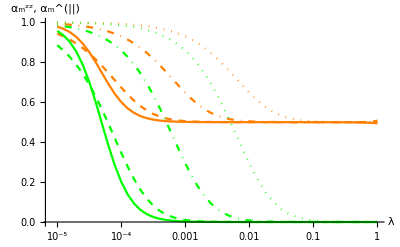

```mathematica
ListLogLinearPlot[curves,
AxesLabel->{"λ","α_m^zz, α_m^(||)"},Joined->True, PlotStyle->
{{Orange, Dotted}, {Orange, DotDashed},{Orange, Dashed},{Orange},
{Green, Dotted},{Green, DotDashed},{Green,Dashed},{Green}}]

ListLogLinearPlot[curves,
AxesLabel->{"λ","α_m^zz, α_m^(||)"},Joined->True, PlotStyle->
{{Orange, Dotted}, {Orange, DotDashed},{Orange, Dashed},{Orange},
{Green, Dotted},{Green, DotDashed},{Green,Dashed},{Green}}]
```

### with vertex corrections

```mathematica
T=Import["~/T.mx"];
MMindex = {2,3,4};
T0 = T[[MMindex,MMindex]];
ClearAll[λ,ϵ,τ,α,Δ]

makeeven[expr_]:=(expr +(expr/.nz->-nz/.nx->-nx))/2
makeodd[expr_]:=(expr -(expr/.nz->-nz/.nx->-nx))/2

myexpr[expr_,μp_,βp_,λp_,αp_]:=Block[{range},
range=range = {μ-15/β,μ+15/β}/.μ->μp/.β->βp;NIntegrate[expr/.{β->βp,λ->λp,α->αp,μ->μp},{ϵ,range[[1]],range[[2]]},Exclusions->{-λp,λp},Method->"DoubleExponential"]
]
SetAttributes[myexpr,Listable];
```

```mathematica
proj = ({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}})-({{nx nx, 0, nx nz, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {nx nz, 0, nz nz, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}});
smallT=proj.T[[{2,3,4,5,9,13},{2,3,4,5,9,13}]]//ReplaceAll[#,{ny->0,nz->0,nx->1,Δ->0}]&//makeeven//ComplexExpand//Simplify

GD[μ_,β_,λ_,α_]:=Block[{tmp,tmp2},tmp = Evaluate@myexpr[smallT,μ,β,λ,α];tmp2=tmp.Inverse[IdentityMatrix[6]-tmp];{tmp2[[2,2]],tmp2[[3,3]]}]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | (π^2 α^2 (2 ϵ^2-3 λ^2) ϵ^2+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | -((π^2 α^2+4) ϵ λ^3)/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | 0
0 | 0 | (π^2 α^2 (ϵ-λ) (ϵ+λ))/(π^2 α^2 ϵ^2+4 λ^2) | 0 | 0 | 0
0 | -((π^2 α^2+4) ϵ λ^3)/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | ((π^2 α^2+4) (π^2 α^2 (ϵ^2-λ^2) ϵ^2+4 λ^2 (ϵ^2-2 λ^2)))/(8 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | 0
((π^2 α^2+4) ϵ λ^3)/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | 0 | 0 | ((π^2 α^2+4) (π^2 α^2 (ϵ^2-λ^2) ϵ^2+4 λ^2 (ϵ^2-2 λ^2)))/(8 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0
0 | 0 | 0 | 0 | 0 | (π^2 α^2)/4)

```mathematica
tmp = myexpr[smallT,μp,βp,0.1,αp];tmp2=tmp.Inverse[IdentityMatrix[6]-tmp];{tmp2[[2,2]],tmp2[[3,3]]}
Clear[tmp,tmp2]
GD[μp,10,0.1,αp]
```

{-3.00095,0.000746063}

Part::partw: Part 3 of … does not exist.

{{(myexpr(makeeven((1)),μp,βp,0.1,αp))/(-2 (myexpr(makeeven((1)),μp,βp,0.1,αp))^2+4+(1-myexpr(makeeven((1)),μp,βp,0.1,αp)) (-2 (myexpr(makeeven((1)),μp,βp,0.1,αp))^2-(1) myexpr(makeeven((1)),μp,βp,0.1,αp)+(-2 1^2-1+(1) 1) 1+(1-myexpr(makeeven((1)),μp,βp,0.1,αp)) (1))),(4+(1-1) (1))/(-2 1^2+4+(1-1) (1)),1,1,1/1,(myexpr(makeeven((1)),μp,βp,0.1,αp))/(-2 (myexpr(makeeven((1)),μp,βp,0.1,αp))^2+(1) myexpr(1)-1+1+(1-myexpr(makeeven((1)),μp,βp,0.1,αp)) (1))},1}
 |  |  |  |

Part::partw: Part 3 of … does not exist.

{{(myexpr(makeeven((1)),μp,10,0.1,αp))/(-2 (myexpr(makeeven((1)),μp,10,0.1,αp))^2+4+(1-myexpr(makeeven((1)),μp,10,0.1,αp)) (-2 (myexpr(makeeven((1)),μp,10,0.1,αp))^2-(1) myexpr(makeeven((1)),μp,10,0.1,αp)+(-2 1^2-1+(1) 1) 1+(1-myexpr(makeeven((1)),μp,10,0.1,αp)) (1))),(4+(1-1) (1))/(-2 1^2+4+(1-1) (1)),1,1,1/1,(myexpr(makeeven((1)),μp,10,0.1,αp))/(-2 (myexpr(makeeven((1)),μp,10,0.1,αp))^2+(1) myexpr(1)-1+1+(1-myexpr(makeeven((1)),μp,10,0.1,αp)) (1))},1}
 |  |  |  |

```mathematica
αp = 10^-4;βp=1;μp=10;
λs = Table[10^n,{n,-5,0,0.1}];
Table[GD[μp,βp,λ,αp]//{λ,#[[1]],λ,#[[2]]}&,{λ,λs}]
```

$Aborted

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (0.00001 | 25.). NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

(0.00001 | -1.0346 | 0.00001 | -1.03472
0.0000125893 | -1.03463 | 0.0000125893 | -1.03478
0.0000158489 | -1.03467 | 0.0000158489 | -1.03486
0.0000199526 | -1.03472 | 0.0000199526 | -1.03496
0.0000251189 | -1.03478 | 0.0000251189 | -1.03508
0.0000316228 | -1.03486 | 0.0000316228 | -1.03524
0.0000398107 | -1.03495 | 0.0000398107 | -1.03544
0.0000501187 | -1.03507 | 0.0000501187 | -1.03569
0.0000630957 | -1.03523 | 0.0000630957 | -1.036
0.0000794328 | -1.03542 | 0.0000794328 | -1.0364
0.0001 | -1.03565 | 0.0001 | -1.0369
0.000125893 | -1.03595 | 0.000125893 | -1.03754
0.000158489 | -1.03632 | 0.000158489 | -1.03836
0.000199526 | -1.03677 | 0.000199526 | -1.03939
0.000251189 | -1.03733 | 0.000251189 | -1.04069
0.000316228 | -1.03802 | 0.000316228 | -1.04236
0.000398107 | -1.03885 | 0.000398107 | -1.04448
0.000501187 | -1.03985 | 0.000501187 | -1.04718
0.000630957 | -1.04103 | 0.000630957 | -1.05066
0.000794328 | -1.04244 | 0.000794328 | -1.05518
0.001 | -1.0441 | 0.001 | -1.06117
0.00125893 | -1.04605 | 0.00125893 | -1.06932
0.00158489 | -1.04833 | 0.00158489 | -1.08078
0.00199526 | -1.05095 | 0.00199526 | -1.09751
0.00251189 | -1.05386 | 0.00251189 | -1.12292
0.00316228 | -1.05694 | 0.00316228 | -1.16328
0.00398107 | -1.06 | 0.00398107 | -1.23087
0.00501187 | -1.06283 | 0.00501187 | -1.35279
0.00630957 | -1.06523 | 0.00630957 | -1.60119
0.00794328 | -1.06712 | 0.00794328 | -2.25291
0.01 | -1.06852 | 0.01 | -6.31514
0.0125893 | -1.06951 | 0.0125893 | 3.40604
0.0158489 | -1.07018 | 0.0158489 | 0.9906
0.0199526 | -1.07063 | 0.0199526 | 0.466452
0.0251189 | -1.07092 | 0.0251189 | 0.25371
0.0316228 | -1.07111 | 0.0316228 | 0.147264
0.0398107 | -1.07122 | 0.0398107 | 0.0884499
0.0501187 | -1.0713 | 0.0501187 | 0.0541649
0.0630957 | -1.07133 | 0.0630957 | 0.0335522
0.0794328 | -1.07138 | 0.0794328 | 0.020929
0.1 | -1.07139 | 0.1 | 0.0131109
0.125893 | -1.07146 | 0.125893 | 0.00823512
0.158489 | -1.07148 | 0.158489 | 0.0051811
0.199526 | -1.07141 | 0.199526 | 0.00326298
0.251189 | -1.07147 | 0.251189 | 0.00205623
0.316228 | -1.07147 | 0.316228 | 0.0012962
0.398107 | -1.07146 | 0.398107 | 0.000817213
0.501187 | -1.07136 | 0.501187 | 0.000515209
0.630957 | -1.07131 | 0.630957 | 0.000324744
0.794328 | -1.07114 | 0.794328 | 0.000204603
1. | -1.06933 | 1. | 0.000128814)

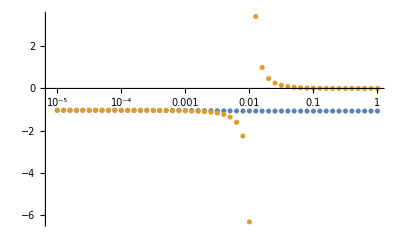

```mathematica
%237;
lists = {Transpose[{λs,(%//Transpose)[[2]]}],Transpose[{λs,(%//Transpose)[[4]]}]}//ListLogLinearPlot[#,PlotRange->All]&
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ϵ in the region (0.1 | 1.50001×10^6). NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

(0.00001 | -1. | 0.00001 | -1.
0.0000125893 | -1. | 0.0000125893 | -1.
0.0000158489 | -1. | 0.0000158489 | -1.
0.0000199526 | -1. | 0.0000199526 | -1.
0.0000251189 | -1. | 0.0000251189 | -1.
0.0000316228 | -1. | 0.0000316228 | -1.
0.0000398107 | -1. | 0.0000398107 | -1.
0.0000501187 | -1. | 0.0000501187 | -1.
0.0000630957 | -1. | 0.0000630957 | -1.
0.0000794328 | -1. | 0.0000794328 | -1.
0.0001 | -1. | 0.0001 | -1.
0.000125893 | -1. | 0.000125893 | -1.
0.000158489 | -1.00001 | 0.000158489 | -1.00001
0.000199526 | -1.00001 | 0.000199526 | -1.00001
0.000251189 | -1.00001 | 0.000251189 | -1.00001
0.000316228 | -1.00001 | 0.000316228 | -1.00001
0.000398107 | -1.00001 | 0.000398107 | -1.00001
0.000501187 | -1.00002 | 0.000501187 | -1.00002
0.000630957 | -1.00002 | 0.000630957 | -1.00002
0.000794328 | -1.00003 | 0.000794328 | -1.00003
0.001 | -1.00003 | 0.001 | -1.00004
0.00125893 | -1.00004 | 0.00125893 | -1.00005
0.00158489 | -1.00006 | 0.00158489 | -1.00006
0.00199526 | -1.00007 | 0.00199526 | -1.00008
0.00251189 | -1.00009 | 0.00251189 | -1.0001
0.00316228 | -1.00012 | 0.00316228 | -1.00013
0.00398107 | -1.00015 | 0.00398107 | -1.00017
0.00501187 | -1.0002 | 0.00501187 | -1.00024
0.00630957 | -1.00026 | 0.00630957 | -1.00032
0.00794328 | -1.00034 | 0.00794328 | -1.00046
0.01 | -1.00044 | 0.01 | -1.00066
0.0125893 | -1.00059 | 0.0125893 | -1.00099
0.0158489 | -1.00079 | 0.0158489 | -1.00155
0.0199526 | -1.00105 | 0.0199526 | -1.00252
0.0251189 | -1.0014 | 0.0251189 | -1.00427
0.0316228 | -1.00185 | 0.0316228 | -1.00755
0.0398107 | -1.00242 | 0.0398107 | -1.01384
0.0501187 | -1.00315 | 0.0501187 | -1.02622
0.0630957 | -1.00405 | 0.0630957 | -1.05126
0.0794328 | -1.00518 | 0.0794328 | -1.10411
0.1 | -1.00659 | 0.1 | -1.22522
0.125893 | -1.00837 | 0.125893 | -1.56172
0.158489 | -1.0106 | 0.158489 | -3.37531
0.199526 | -1.01342 | 0.199526 | 2.69269
0.251189 | -1.01698 | 0.251189 | 0.606154
0.316228 | -1.02149 | 0.316228 | 0.247067
0.398107 | -1.02722 | 0.398107 | 0.118895
0.501187 | -1.03454 | 0.501187 | 0.0624047
0.630957 | -1.04387 | 0.630957 | 0.0349589
0.794328 | -1.05587 | 0.794328 | 0.020794
1. | -1.07139 | 1. | 0.0131109)

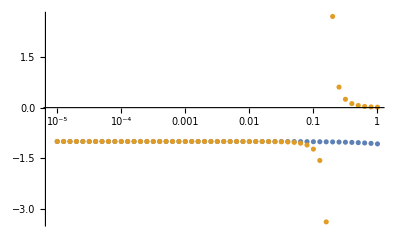

```mathematica
αp = 10^-4;λp=0.1;βp=1;μp=10;
βs = Table[10^n,{n,-5,0,0.1}];
Table[GD[μp,β,λp,αp]//{β,#[[1]],β,#[[2]]}&,{β,βs}]
lists = {Transpose[{λs,(%//Transpose)[[2]]}],Transpose[{λs,(%//Transpose)[[4]]}]}//ListLogLinearPlot[#,PlotRange->All]&
```

```mathematica
NotebookSave[]
```

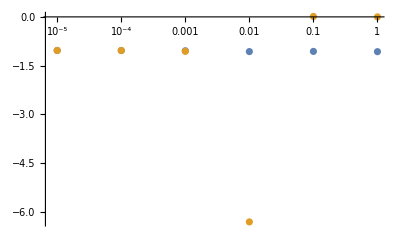

```mathematica
{Transpose[{λs,(%196//Transpose)[[1]]}],Transpose[{λs,(%196//Transpose)[[2]]}]}//ListLogLinearPlot[#,PlotRange->All]&
```

```mathematica
smallT[[{{2,2},{3,3}}]]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | (π^2 α^2 (2 ϵ^2-3 λ^2) ϵ^2+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | -((π^2 α^2+4) ϵ λ^3)/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | 0
0 | 0 | (π^2 α^2 (ϵ-λ) (ϵ+λ))/(π^2 α^2 ϵ^2+4 λ^2) | 0 | 0 | 0
0 | -((π^2 α^2+4) ϵ λ^3)/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | ((π^2 α^2+4) (π^2 α^2 (ϵ^2-λ^2) ϵ^2+4 λ^2 (ϵ^2-2 λ^2)))/(8 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | 0
((π^2 α^2+4) ϵ λ^3)/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | 0 | 0 | ((π^2 α^2+4) (π^2 α^2 (ϵ^2-λ^2) ϵ^2+4 λ^2 (ϵ^2-2 λ^2)))/(8 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0
0 | 0 | 0 | 0 | 0 | (π^2 α^2)/4)⟦{2;;2}⟧

Part::pkspec1: The expression (2 | 2
3 | 3) cannot be used as a part specification.

(0 | 0 | 0 | 0 | 0 | 0
0 | (π^2 α^2 (2 ϵ^2-3 λ^2) ϵ^2+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | -((π^2 α^2+4) ϵ λ^3)/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | 0
0 | 0 | (π^2 α^2 (ϵ-λ) (ϵ+λ))/(π^2 α^2 ϵ^2+4 λ^2) | 0 | 0 | 0
0 | -((π^2 α^2+4) ϵ λ^3)/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | ((π^2 α^2+4) (π^2 α^2 (ϵ^2-λ^2) ϵ^2+4 λ^2 (ϵ^2-2 λ^2)))/(8 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | 0
((π^2 α^2+4) ϵ λ^3)/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0 | 0 | 0 | ((π^2 α^2+4) (π^2 α^2 (ϵ^2-λ^2) ϵ^2+4 λ^2 (ϵ^2-2 λ^2)))/(8 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2)) | 0
0 | 0 | 0 | 0 | 0 | (π^2 α^2)/4)⟦(2 | 2
3 | 3)⟧

```mathematica
tmp/.ϵ->160
```

3.0566×10^-8

```mathematica
coeff[αs,expr1p/.λ->0.1, 0.1]
```

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at ϵ = 160..

General::stop: Further output of NIntegrate::ncvs will be suppressed during this calculation.

{Null,Null,Null,Null}

```mathematica
β=0.1
tmp = expr1p//.{μ->10,Δ->0,nz->0,nx->1}/.{α->αp}
range = {μ-15/β,μ+15/β}/.μ->10
NIntegrate[tmp/.λ->0.1,{ϵ,range[[1]],range[[2]]},Exclusions->{λ,-λ},Method->"DoubleExponential"]
```

0.1

(0.05 ⅇ^(0.1 (-10+ϵ)) (π^2 αp^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2)))/((1+ⅇ^(0.1 (-10+ϵ)))^2 (ϵ-λ) (ϵ+λ) (π^2 αp^2 ϵ^2+4 λ^2))

{-140.,160.}

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at ϵ = 160..

General::stop: Further output of NIntegrate::ncvs will be suppressed during this calculation.

NIntegrate[tmp/.λ→0.1,{ϵ,range⟦1⟧,range⟦2⟧},Exclusions→{λ,-λ},Method→DoubleExponential]